```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Marchevsky\VM2D\VM2D\settings\airfoils

```mathematica
n=100;
```

```mathematica
Pts=N[Table[N[1/2{Cos[(2π)/n(i-1.0)],Sin[(2π)/n(i-1.0)]}],{i,1,n}],16];
```

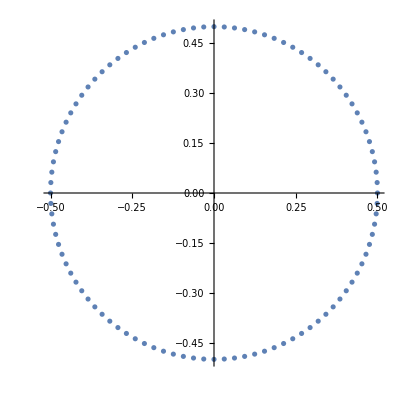

```mathematica
ListPlot[Pts,AspectRatio->Automatic]
```

```mathematica
Export["circle"<>ToString[n],
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.9    |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2020/07/22     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2020 Ilia Marchevsky, Kseniia Kuzmina, Evgeniya Ryatina  |
*-----------------------------------------------------------------------------*
| File name: circle"<>TextString[n]<>StringRepeat[" ",59-StringLength@ToString[n]]<>"|
| Info: Circular airfoil ("<>TextString[n]<>" panels)"<>StringRepeat[" ",44-StringLength@ToString[n]]<>"|
\\*---------------------------------------------------------------------------*/
"}~Join~{"r = {"}~Join~((TextString[#]<>",")&/@(Pts[[1;;-2]]))~Join~((TextString[#])&/@(Pts[[{-1}]]))~Join~{" };"},"Table"]
```

circle100